```mathematica
SetDirectory["~/Dropbox/Posttraumatic Medoids Disorder/CodeForPaper/"]
```

/Users/anellore/Dropbox/Posttraumatic Medoids Disorder/CodeForPaper

```mathematica
failpts2 = Import["fail_pts_2balls.csv"];failsoln2=Import["fail_soln_2balls.csv"];successpts2=Import["success_pts_2balls.csv"];successsoln2 = Import["success_soln_2balls.csv"];failpts3 = Import["fail_pts_3balls.csv"];failsoln3=Import["fail_soln_3balls.csv"];successpts3=Import["success_pts_3balls.csv"];successsoln3= Import["success_soln_3balls.csv"];
```

```mathematica
successclusters3=DeleteDuplicates[successsoln3];successcluster31 = successpts3[[Flatten[Position[successsoln3,successclusters3[[1]]]]]];successcluster32=successpts3[[Flatten[Position[successsoln3,successclusters3[[2]]]]]];successcluster33=successpts3[[Flatten[Position[successsoln3,successclusters3[[3]]]]]];successclusters3medoids=successpts3[[Position[successclusters3, 1][[All,2]]]];
```

```mathematica
successclusters2=DeleteDuplicates[successsoln2];successcluster21 = successpts2[[Flatten[Position[successsoln2,successclusters2[[1]]]]]];successcluster22=successpts2[[Flatten[Position[successsoln2,successclusters2[[2]]]]]];successclusters2medoids=successpts2[[Position[successclusters2, 1][[All,2]]]];
```

```mathematica
failclusters3=DeleteDuplicates[failsoln3];failcluster31 = failpts3[[Flatten[Position[failsoln3,failclusters3[[1]]]]]];failcluster32=failpts3[[Flatten[Position[failsoln3,failclusters3[[2]]]]]];failcluster33=failpts3[[Flatten[Position[failsoln3,failclusters3[[3]]]]]];failclusters3medoids=failpts3[[Position[failclusters3, 1][[All,2]]]];
```

```mathematica
failclusters2=DeleteDuplicates[failsoln2];failcluster21 = failpts2[[Flatten[Position[failsoln2,failclusters2[[1]]]]]];failcluster22=failpts2[[Flatten[Position[failsoln2,failclusters2[[2]]]]]];failclusters2medoids=failpts2[[Position[failclusters2, 1][[All,2]]]];
```

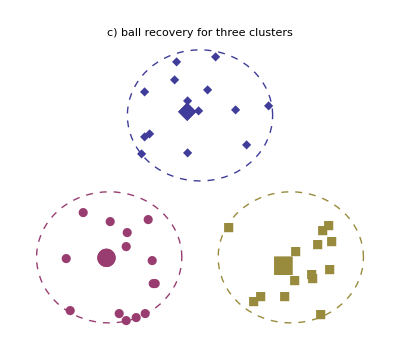

```mathematica
s3=Show[ListPlot[{successcluster31,successcluster32,successcluster33,{successclusters3medoids[[1]]},{successclusters3medoids[[2]]},{successclusters3medoids[[3]]}}, PlotMarkers->{{"●", 12},{"■",12},{"◆",12},{"●",24},{"■",24},{"◆",24}}, PlotStyle->{ColorData[1,2],ColorData[1,3],ColorData[1,1]}, Axes->None,Frame->False,FrameStyle->{Directive[FontFamily->"Futura", FontSize->12,Black], Directive[FontFamily->"Futura", FontSize->12] }],Graphics[{ColorData[1,2],Dashed,Thick,Circle[{0,0}]}], Graphics[{ColorData[1,3],Dashed,Thick,Circle[{2.5,0}]}],Graphics[{ColorData[1,1],Dashed,Thick,Circle[{2.5/2,2.5/2 * Sqrt[3]}]}], PlotRange->All, AspectRatio->4/4.5,PlotLabel->Style["c) ball recovery for three clusters", FontFamily->"Futura", FontSize->17, RGBColor[227/256,29/256,118/256]]]
```

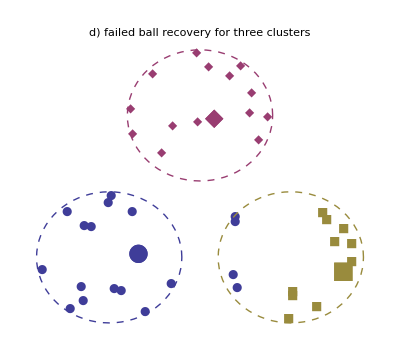

```mathematica
f3=Show[ListPlot[{failcluster31,failcluster32,failcluster33,{failclusters3medoids[[1]]},{failclusters3medoids[[2]]},{failclusters3medoids[[3]]}}, PlotMarkers->{{"●", 12},{"■",12},{"◆",12},{"●",24},{"■",24},{"◆",24}}, PlotLabel->Style["d) failed ball recovery for three clusters", FontFamily->"Futura", FontSize->17,RGBColor[227/256,29/256,118/256]],PlotStyle->{ColorData[1,1],ColorData[1,3],ColorData[1,2]}, Axes->None,Frame->False],  Graphics[{ColorData[1,1],Dashed,Thick,Circle[{0,0}]}],Graphics[{ColorData[1,3],Dashed,Thick,Circle[{2.5,0}]}],Graphics[{ColorData[1,2],Dashed,Thick,Circle[{2.5/2,2.5/2 * Sqrt[3]}]}], PlotRange->All, AspectRatio->4/4.5]
```

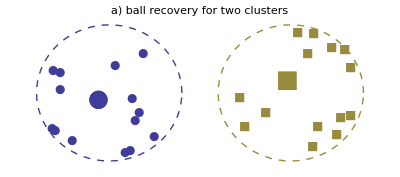

```mathematica
s2=Show[ListPlot[{successcluster21,successcluster22,{successclusters2medoids[[1]]},{successclusters2medoids[[2]]}}, PlotMarkers->{{"●", 12},{"■",12},{"●",24},{"■",24}}, PlotStyle->{ColorData[1,1],ColorData[1,3]}, Axes->None,Frame->False,FrameStyle->{Directive[FontFamily->"Futura", FontSize->12,Black], Directive[FontFamily->"Futura", FontSize->12] },PlotLabel->Style["a) ball recovery for two clusters", FontFamily->"Futura", FontSize->17,RGBColor[227/256,29/256,118/256]]],Graphics[{ColorData[1,1],Dashed,Thick,Circle[{0,0}]}], Graphics[{ColorData[1,3],Dashed,Thick,Circle[{2.5,0}]}],PlotRange->All, AspectRatio->2/4.5]
```

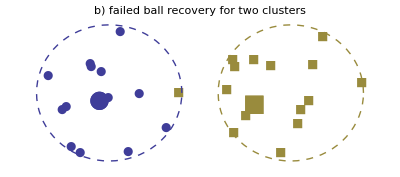

```mathematica
f2=Show[ListPlot[{failcluster21,failcluster22,{failclusters2medoids[[1]]},{failclusters2medoids[[2]]}}, PlotMarkers->{{"●", 12},{"■",12},{"●",24},{"■",24}},FrameStyle->{Directive[FontFamily->"Futura", FontSize->12,Black], Directive[FontFamily->"Futura", FontSize->12] },PlotStyle->{ColorData[1,1],ColorData[1,3]}, Axes->None,Frame->False],Graphics[{ColorData[1,1],Dashed,Thick,Circle[{0,0}]}], Graphics[{ColorData[1,3],Dashed,Thick,Circle[{2.5,0}]}],PlotRange->All, AspectRatio->2/4.5, PlotLabel->Style["b) failed ball recovery for two clusters", FontFamily->"Futura", FontSize->17,RGBColor[227/256,29/256,118/256]]]
```

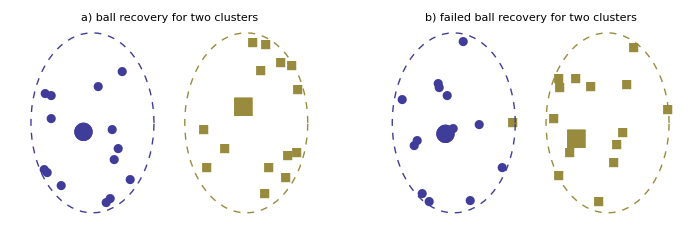

```mathematica
plottop=GraphicsGrid[{{s2,f2}}, ImageSize->{700,234},PlotLabel->Style[Grid[{{"successful and failed 2-ball recoveries for R = 2.5"},{"n = 15 points drawn from each ball (dashed) are independent samples of uniform distribution"}, {"points in same cluster have same marker and color; medoids are large points"}}],15, FontFamily->"Futura"], Dividers->{{False, Directive[Dashed,RGBColor[227/256,29/256,118/256]], False}, {False,False}}]
```

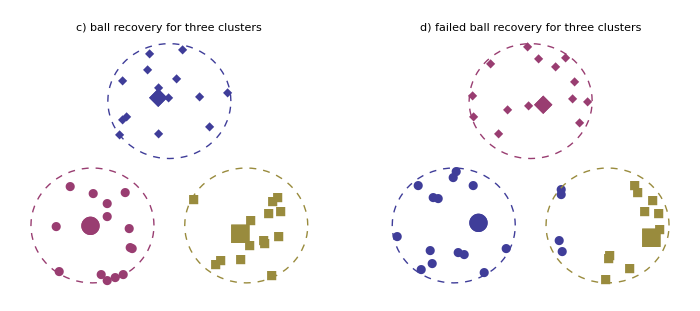

```mathematica
plotbottom=GraphicsGrid[{{s3,f3}}, ImageSize->{700,311},Dividers->{{False, Directive[Dashed,RGBColor[227/256,29/256,118/256]], False}, { Directive[Dashed,RGBColor[227/256,29/256,118/256]],False}}]
```

```mathematica
Export["failtop.pdf",plottop,"AllowRasterization"->True,ImageResolution->600]
```

failtop.pdf

```mathematica
Export["failbottom.pdf",plotbottom,"AllowRasterization"->True,ImageResolution->600]
```

failbottom.pdf